{{0,1,0,1,0,1,0,0,0,0,0,0,0},{1,0,0,1,0,1,0,0,0,0,0,0,0},{0,0,0,0,1,0,1,1,1,0,0,1,0},{1,1,0,0,0,1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,1,0,0,0,0,1},{1,1,0,1,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,1,1,0,0,1,0},{0,0,1,0,1,0,1,0,0,0,0,0,0},{0,0,1,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,1,0,0,0}}

{{3.25}}

3.25

4

{{13}}

13

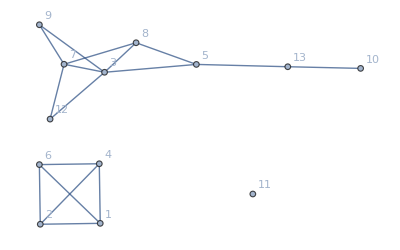

A is: {{6,8,9,11,12,13},{4,8,9,11,12,13},{2,8,9,11,12,13},{1,8,9,11,12,13},{6,8,9,10,11,12},{4,8,9,10,11,12},{2,8,9,10,11,12},{1,8,9,10,11,12},{5,6,9,10,11,12},{4,5,9,10,11,12},{2,5,9,10,11,12},{1,5,9,10,11,12},{5,6,7,10,11},{4,5,7,10,11},{2,5,7,10,11},{1,5,7,10,11},{6,7,11,13},{4,7,11,13},{2,7,11,13},{1,7,11,13},{3,6,11,13},{3,4,11,13},{2,3,11,13},{1,3,11,13},{3,6,10,11},{3,4,10,11},{2,3,10,11},{1,3,10,11}}

result is: {{6,8,9,11,12,13}}

isolated is: {1,2,3,4,5,7,10}

we are at Length[isolated]≠0

resultnew is: {{6,8,9,11,12,13}}

we are at resultnew==result

indepFromIsolated is: {{4,5,7,10},{2,5,7,10},{1,5,7,10},{3,4,10},{2,3,10},{1,3,10}}

inddisjointfromIsolated is: {{4,5,7,10}}

we are at complete append

joined result is:{{6,8,9,11,12,13},{4,5,7,10}}

new isolated is: {1,2,3}

we are at Length[isolated]≠0

resultnew is: {{6,8,9,11,12,13},{4,5,7,10}}

we are at resultnew==result

indepFromIsolated is: {{2,3},{1,3}}

inddisjointfromIsolated is: {{2,3}}

we are at complete append

joined result is:{{6,8,9,11,12,13},{4,5,7,10},{2,3}}

new isolated is: {1}

we are at Length[isolated]≠0

resultnew is: {{6,8,9,11,12,13},{4,5,7,10},{2,3}}

we are at resultnew==result

indepFromIsolated is: {{1}}

inddisjointfromIsolated is: {{1}}

we are at complete append

joined result is:{{6,8,9,11,12,13},{4,5,7,10},{2,3},{1}}

new isolated is: {}

we are at Length[result]≥resources

we are at resultcopy calculation

we just generated resultfinal

resultfinal is: {{1},{2,3},{4,5,7,10},{6,8,9,11,12,13}}

```mathematica
(* Import the connectivity matrix "D2D-connectivity-matrix.txt", generated in Matlab, in order to make the independent subsets of quantity "LI" *)
W=Import["Desktop/Script_Files/Matlab/D2D/ExtensionBatchRateAdjustmentDynamicFinalnodelayMinorChanges/D2D-connectivity-matrix.txt","Table"]

(* we import the "LI", generated in Matlab, in order to make the independent subsets of size "LI" *)
LI=Import["Desktop/Script_Files/Matlab/D2D/ExtensionBatchRateAdjustmentDynamicFinalnodelayMinorChanges/LI.txt","Table"]
(* we take out unnecessary {{}} of LI *)
LI=LI[[1,1]]
LI=Ceiling[LI]

(* In this script we need to have the "LI_T", since we need to compare it with "LI" and take the decision  *)
LIT=3;

(* In this script we consider the "resources" constant, since in Matlab side we don't do any modification to the number of resources *)
resources=4;

(* we import the "numberOfBG", from Matlab, in order to check the presence of all BGs in the generated disjoint independent subset "result" *)
numberOfBG=Import["Desktop/Script_Files/Matlab/D2D/ExtensionBatchRateAdjustmentDynamicFinalnodelayMinorChanges/numberOfBG.txt","Table"]
numberOfBG=numberOfBG[[1,1]]
BGoriginal=Range[numberOfBG];
BG=ConstantArray[0,numberOfBG];

(* to present the graph *)
W1=AdjacencyGraph[W,VertexLabels->"Name"]

(* We first find all the maximum independent subsets of size "LI" *)
A=FindIndependentVertexSet[W1,{LI,numberOfBG},All];
Print["A is: ", A]

(* The following function gets first list with removed all elements from second list which are present in first list *)
removeFrom[b_List,a_List]:=Module[{f},f[_]=0;
(f[#]=-#2)&@@@Tally[a];
Pick[b,UnitStep[f[#]++&/@b],1]];


(* The followings are all functions defined, in order to select from "A", just all the disjoint ones, in different ways; I test to see which one covers all the nodes of the graph *)
maximalDisjointSubset[list_]:=Module[{vertices=Range@Length@list,edges},edges=Cases[Subsets[vertices,2],{i_,j_}/;Intersection@@list[[{i,j}]]≠{}:>i<->j];
list[[First@FindIndependentVertexSet@Graph[vertices,edges]]]];

fn1=Module[{ms=Subsets[#,{2,Length@#}]},Take[Reverse[Pick[ms,And@@DisjointQ@@@Subsets[#,{2}]&/@ms]],UpTo[1]]]&;

fn2=Module[{ms=Subsets[#,{2,Length@#}]},Pick[ms,And@@DisjointQ@@@Subsets[#,{2}]&/@ms]]&;
(* Now we put "A" in it to generate the results *)
result=maximalDisjointSubset[A];
Print["result is: ",result]

(* We save the "result" with a new name to be intact in case needed for the rate adjustment; the same is applicable for the isloated *)
originalresult=result;

isolated=ConstantArray[0,numberOfBG];
Do[If[FreeQ[result,i],isolated[[i]]=i],{i,1,numberOfBG}];
isolated=DeleteCases[isolated,0];
Print["isolated is: ", isolated]
originalisolated=isolated;

(* The following function lists positions of all duplicate elements of a list. this is needed to be applied to "myvertices" list later, because we will replace all duplicate elements of it with 0, except the first occurence. then we generate "mypositions" out of it. I've no longer used this function, because I used a simpler way of doing the same thing *)
positionDuplicates[list_]:=GatherBy[Range@Length[list],list[[#]]&];
(*duplicates=Select[duplicates,Length[#]>1&];*)


(* In the following nested Do loop, we test if adding elements from list "isolated" to elements of "result" still keeps that element of "result" an independent subset of graph W1; If so, we add that element from "isolated" to that element of "result", otherwise we don't and we test the other element of "result", till the end *)
(* First we create a duplciate of "result" named as resultnew *)

(* Corrected the big If statement *)

Label["top"];If[Length[result]≥resources,Print["we are at Length[result]≥resources"];result=Sort[result];extras=Length[result]- resources;If[extras>0,Do[isolated=Append[isolated,result[[i]]],{i,1,Length[extras]}];result=Drop[result,extras];];Print["we are at resultcopy calculation"];
Do[
tempresult=result;
tempresultedges=ConstantArray[0,Length[result]];
Do[
Part[tempresult,n]=Append[Part[tempresult,n],isolated[[m]]];
Part[tempresultedges,n]=EdgeCount[Subgraph[W1,Part[tempresult,n],VertexLabels->"Name"]];
,{n,1,Length[result]}];
Print["tempresult is: ", tempresult];
Print["tempresultedges is: ", tempresultedges];
Part[result,Position[tempresultedges,Min[tempresultedges]][[1,1]]]=Part[tempresult,Position[tempresultedges,Min[tempresultedges]][[1,1]]];
,{m,1,Length[isolated]}];Do[If[MemberQ[result,l],BG=ReplacePart[BG,l->l]],{l,1,numberOfBG}];
resultfinal=result;Print["we just generated resultfinal"];

,Print["we are at Length[isolated]≠0"];If[Length[isolated]≠0,resultnew=result;
Do[If[IndependentVertexSetQ[W1,Append[resultnew[[j]],isolated[[i]]]],resultnew[[j]]=Append[resultnew[[j]],isolated[[i]]]],{i,1,Length[isolated]},{j,1,Length[result]}];Print["resultnew is: ", resultnew];

If[resultnew==result,Print["we are at resultnew==result"];indepFromIsolated=FindIndependentVertexSet[Subgraph[W1,isolated,VertexLabels->"Name"],{1,Length[isolated]},All];
Print["indepFromIsolated is: ", indepFromIsolated];
inddisjointfromIsolated=maximalDisjointSubset[indepFromIsolated];Print["inddisjointfromIsolated is: ", inddisjointfromIsolated];If[(Length[result]+Length[inddisjointfromIsolated])≤resources,Print["we are at complete append"];result=Join[result,inddisjointfromIsolated];Print["joined result is:", result];,



Print["we are at opposite to complete append"];x=resources-Length[result];temp1=Sort[inddisjointfromIsolated];Print["temp1=Sort[inddisjointfromIsolated] is: ", temp1];
OrderedinddisjointfromIsolated=Reverse[temp1];Print["reverse temp1=Sort[inddisjointfromIsolated] is: ", OrderedinddisjointfromIsolated];Do[result=Append[result,OrderedinddisjointfromIsolated[[i]]],{i,1,x}];Print["we are at result with partly appended isolated is: ", result];result=Sort[result];
];

Do[If[MemberQ[result,l],BG=ReplacePart[BG,l->l]],{l,1,numberOfBG}];      

If[BG==BGoriginal,resultfinal=result,goneelements=Intersection[Flatten[result],Flatten[isolated]];isolated=removeFrom[isolated,goneelements];Print["new isolated is: ", isolated];

Goto["top"]; 
];

,

Do[If[MemberQ[resultnew,l],BG=ReplacePart[BG,l->l]],{l,1,numberOfBG}];If[BG==BGoriginal,resultfinal=resultnew,result=resultnew;goneelements=Intersection[Flatten[resultnew],Flatten[isolated]];isolated=removeFrom[isolated,goneelements];
indepFromIsolated=FindIndependentVertexSet[Subgraph[W1,isolated,VertexLabels->"Name"],{1,Length[isolated]},All];
Print["indepFromIsolated is: ", indepFromIsolated];
inddisjointfromIsolated=maximalDisjointSubset[indepFromIsolated];Print["inddisjointfromIsolated is: ", inddisjointfromIsolated];If[(Length[result]+Length[inddisjointfromIsolated])≤resources,result=Append[result,inddisjointfromIsolated],x=resources-Length[result];temp1=Sort[inddisjointfromIsolated];
OrderedinddisjointfromIsolated=Reverse[temp1];Do[result=Append[result,OrderedinddisjointfromIsolated[[i]]],{i,1,x}];result=Sort[result];
result[[1]]=Append[result[[1]],Part[OrderedinddisjointfromIsolated,-(Length[OrderedinddisjointfromIsolated]-x)][[1]]];
];resultfinal=result]];,resultfinal=result]];

Do[Part[resultfinal,i]=DeleteDuplicates[Part[resultfinal,i]],{i,1,Length[resultfinal]}];
Print["resultfinal is: ",resultfinal];


(* Here is the point we test to see if rate adjustment is needed or not *)
(
Goto[noadjust]; 
Label[withadjustmentnow];
(****** The following lines would be used in case of rate adjustment, otherwise not ******)
 LI=LIT;
   newD2DresourcesSRBCell1=numberOfBG/LIT;
   newD2DresourcesSRBCell1=Ceiling[newD2DresourcesSRBCell1];
(* find the nr of resources at bottom and top of 1 subframe,with 50
RBs.we'll have "xSRB" resources at bottom and "xSRB" resources at top *)
xSRB=newD2DresourcesSRBCell1/2;
  xSRB=Ceiling[xSRB];
  newD2DresourcesSRBCell1=2*(xSRB);
(* since D2Dresources (at each side(bottom/top):10 in terms of RBs) is constant,we have newLCRBD2D as: *)
  newLCRBCell1=10/xSRB; 
newLCRBCell1=floor(newLCRBCell1);
(* determine the NEW total nr of resources,in terms of SRBs:resources for D2D(2*xSRB)+resources for CUEs(6) *)
nrResourcesTotalCell1=(2*xSRB)+6;
(* We set "resources" equal to the new number of resources, in order to run again the loop for disjoint independent subset geenration, in case of the rate adjustment *)
newresources=newD2DresourcesSRBCell1;

(* By using the saved "originalresult" & "originalisolated", we run the above big if statement again to produce the new result with new number of resources, just created in the above line ; note that we rename the original "result" and "isolated" and "newresources" here in order to use the previous piece of code without change *)
result=originalresult;
isolated=originalisolated;
resources=newresources;

Label["top2"];If[Length[result]≥resources,Print["we are at Length[result]≥resources"];result=Sort[result];extras=Length[result]- resources;If[extras>0,Do[isolated=Append[isolated,result[[i]]],{i,1,Length[extras]}];result=Drop[result,extras];];Print["we are at resultcopy calculation"];
Do[
tempresult=result;
tempresultedges=ConstantArray[0,Length[result]];
Do[
Part[tempresult,n]=Append[Part[tempresult,n],isolated[[m]]];
Part[tempresultedges,n]=EdgeCount[Subgraph[W1,Part[tempresult,n],VertexLabels->"Name"]];
,{n,1,Length[result]}];
Print["tempresult is: ", tempresult];
Print["tempresultedges is: ", tempresultedges];
Part[result,Position[tempresultedges,Min[tempresultedges]][[1,1]]]=Part[tempresult,Position[tempresultedges,Min[tempresultedges]][[1,1]]];
,{m,1,Length[isolated]}];Do[If[MemberQ[result,l],BG=ReplacePart[BG,l->l]],{l,1,numberOfBG}];
resultfinal=result;Print["we just generated resultfinal"];

,Print["we are at Length[isolated]≠0"];If[Length[isolated]≠0,resultnew=result;
Do[If[IndependentVertexSetQ[W1,Append[resultnew[[j]],isolated[[i]]]],resultnew[[j]]=Append[resultnew[[j]],isolated[[i]]]],{i,1,Length[isolated]},{j,1,Length[result]}];Print["resultnew is: ", resultnew];

If[resultnew==result,Print["we are at resultnew==result"];indepFromIsolated=FindIndependentVertexSet[Subgraph[W1,isolated,VertexLabels->"Name"],{1,Length[isolated]},All];
Print["indepFromIsolated is: ", indepFromIsolated];
inddisjointfromIsolated=maximalDisjointSubset[indepFromIsolated];Print["inddisjointfromIsolated is: ", inddisjointfromIsolated];If[(Length[result]+Length[inddisjointfromIsolated])≤resources,Print["we are at complete append"];result=Join[result,inddisjointfromIsolated];Print["joined result is:", result];,



Print["we are at opposite to complete append"];x=resources-Length[result];temp1=Sort[inddisjointfromIsolated];Print["temp1=Sort[inddisjointfromIsolated] is: ", temp1];
OrderedinddisjointfromIsolated=Reverse[temp1];Print["reverse temp1=Sort[inddisjointfromIsolated] is: ", OrderedinddisjointfromIsolated];Do[result=Append[result,OrderedinddisjointfromIsolated[[i]]],{i,1,x}];Print["we are at result with partly appended isolated is: ", result];result=Sort[result];
];

Do[If[MemberQ[result,l],BG=ReplacePart[BG,l->l]],{l,1,numberOfBG}];      

If[BG==BGoriginal,resultfinal=result,goneelements=Intersection[Flatten[result],Flatten[isolated]];isolated=removeFrom[isolated,goneelements];Print["new isolated is: ", isolated];

Goto["top2"]; 
];

,

Do[If[MemberQ[resultnew,l],BG=ReplacePart[BG,l->l]],{l,1,numberOfBG}];If[BG==BGoriginal,resultfinal=resultnew,result=resultnew;goneelements=Intersection[Flatten[resultnew],Flatten[isolated]];isolated=removeFrom[isolated,goneelements];
indepFromIsolated=FindIndependentVertexSet[Subgraph[W1,isolated,VertexLabels->"Name"],{1,Length[isolated]},All];
Print["indepFromIsolated is: ", indepFromIsolated];
inddisjointfromIsolated=maximalDisjointSubset[indepFromIsolated];Print["inddisjointfromIsolated is: ", inddisjointfromIsolated];If[(Length[result]+Length[inddisjointfromIsolated])≤resources,result=Append[result,inddisjointfromIsolated],x=resources-Length[result];temp1=Sort[inddisjointfromIsolated];
OrderedinddisjointfromIsolated=Reverse[temp1];Do[result=Append[result,OrderedinddisjointfromIsolated[[i]]],{i,1,x}];result=Sort[result];
result[[1]]=Append[result[[1]],Part[OrderedinddisjointfromIsolated,-(Length[OrderedinddisjointfromIsolated]-x)][[1]]];
];resultfinal=result]];,resultfinal=result]];

Do[Part[resultfinal,i]=DeleteDuplicates[Part[resultfinal,i]],{i,1,Length[resultfinal]}];
Print["resultfinal is: ",resultfinal];

(****** The above lines would be used in case of rate adjustment, otherwise not ******)

(* The following for loop is different from the loop in other versions of this file, in a sense that here we apply the rate adjustment, while in others we do not have the rate adjustment *)
(* The strcture of the following big if statement is : If[LI<=LIT,keep the same,If[Length[result]<=resources,keep the same,adjust]]; *)

Label[noadjust];
If[LI<=LIT,resultfinal=result,edgenr=0;Do[edge=EdgeCount[Subgraph[W1,result[[i]],VertexLabels->"Name"]];If[edge≠0,edgenr=edgenr+1;],{i,1,Length[result]}];If[edgenr==0,resultfinal=result,Print["we do rate adjustment"];Goto[withadjustmentnow];]];

)
(* Note that (with the current max number of BGs as 20) it's quite unlikely that after one time rate adjustment, we still have non-independent subsets; so, it's unlikely that the code falls in an infinite loop *)



(* The following line exports all the independent subsets, into separate files *)
(*Do[Export["Desktop/Script_Files/Matlab/D2D/extended version2/disjointset"<>ToString[i]<>".txt",result[[i]]],{i,1,Length[result]}]*)
(* The following line exports all the independent subsets together *)
(*Export["Desktop/Script_Files/Matlab/D2D/ExtensionBatchRateAdjustmentDynamicFinalnodelayMinorChanges/DisjointIndependentSubsets.txt",result]*)
Export["Desktop/Script_Files/Matlab/D2D/ExtensionBatchRateAdjustmentDynamicFinalnodelayMinorChanges/DisjointIndependentSubsetsDynamicK"<> ToString[19]<>"T"<>ToString[13]<>".txt",resultfinal,"Table","FieldSeparators"->" "]
```

```mathematica
"Desktop/Script_Files/Matlab/D2D/ExtensionBatchRateAdjustmentDynamicFinalnodelayMinorChanges/DisjointIndependentSubsetsDynamicK19T13.txt"
```

```mathematica
"Desktop/Script_Files/Matlab/D2D/ExtensionBatchRateAdjustmentDynamicFinalnodelayMinorChanges/DisjointIndependentSubsetsDynamicraterep10.txt"
```

```mathematica
"Desktop/Script_Files/Matlab/D2D/ExtensionBatchRateAdjustmentDynamicFinalnodelayMinorChanges/DisjointIndependentSubsetsDynamicraterep10.txt"
```

```mathematica
"Desktop/Script_Files/Matlab/D2D/ExtensionBatchRateAdjustmentDynamicFinalnodelayMinorChanges/DisjointIndependentSubsetsDynamic.txt"
```

```mathematica
"Desktop/Script_Files/Matlab/D2D/ExtensionBatchRateAdjustmentDynamicFinalnodelayMinorChanges/DisjointIndependentSubsetsDynamic.txt"
```

```mathematica
"Desktop/Script_Files/Matlab/D2D/ExtensionBatchRateAdjustmentDynamicFinalnodelayMinorChanges/DisjointIndependentSubsetsDynamic.txt"
```

```mathematica
"Desktop/Script_Files/Matlab/D2D/ExtensionBatchRateAdjustmentDynamicFinalnodelayMinorChanges/DisjointIndependentSubsetsDynamic.txt"
```